```mathematica
ClearAll["Global`*"]
(*$PrePrint=If[MatrixQ@#,MatrixForm@#,#]&;*)
(*This code is supposed to find the Transformation stretch tensor for Tetragonal to Triclinic*)
```

```mathematica
(*The problem with this is that I did this for only 1 correspondence. There would be multiple correspondences. One needs to check that. Check the later file titled "LSCO-Tetragonal2Monoclinic".Also didnt consider the rotation here. Check polar decomposition method of determining the minimizing rotation.*)
```

```mathematica
(*Defining the refernce {f_i} and deformed {u_i} basis vectors*)
f1:={a0,0,0}
f2:={0,a0,0}
f3:={0,0,c0}
u1:={a,0,0}
u2:={b*Cos[γ],b*Sin[γ],0}
u3:={c*Cos[β],c/Sin[γ]*(Cos[α]-Cos[γ]*Cos[β]),c/Sin[γ]*Sqrt[Sin[β]^2*Sin[γ]^2-Cos[β]^2*Cos[γ]^2-Cos[α]^2+2*Cos[α]*Cos[β]*Cos[γ]]}
```

```mathematica
(*Defining the reference dual and checking that it makes sense.*)
rf1:={1/a0,0,0}
rf2:={0,1/a0,0}
rf3:={0,0,1/c0}
{{rf1.f1,rf1.f2,rf1.f3},{rf2.f1,rf2.f2,rf2.f3},{rf3.f1,rf3.f2,rf3.f3}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Checking if the deofmred basis vectors are correct*)
{u1.u1,u1.u2,u1.u3,u2.u2,u2.u3,u3.u3}//Simplify
```

{a^2,a b Cos[γ],a c Cos[β],b^2,b c Cos[α],c^2}

```mathematica
(*Determining the Stretch tenosr*)
F:=Outer[Times,u1,rf1]+Outer[Times,u2,rf2]+Outer[Times,u3,rf3]
Print["F=",F//MatrixForm]
UI:=Sqrt[Transpose[F].F](*This is incorrect, should be replaced by MatrixPower. Check if DetQ=1*)
Print["U=√(F^T F)=",UI//MatrixForm//Simplify]
Print["||UI-UI^T||=",Norm[UI-Transpose[UI]]](*making sure that U is symm*)
Print["||F^TF-UI^2||=",Norm[Transpose[F].F-UI^2]](*Making sure that U^2=F^TF*)
Q:=F.Inverse[UI]
(*Print["Q=",Q//MatrixForm//Simplify]*)
Print["Det(Q)=",Det[Q]//Simplify//PowerExpand]
```

F=(a/a0 | (b Cos[γ])/a0 | (c Cos[β])/c0
0 | (b Sin[γ])/a0 | (c (Cos[α]-Cos[β] Cos[γ]) Csc[γ])/c0
0 | 0 | (c Csc[γ] √(-Cos[α]^2+2 Cos[α] Cos[β] Cos[γ]-Cos[β]^2 Cos[γ]^2+Sin[β]^2 Sin[γ]^2))/c0)

U=√(F^T F)=(√(a^2/a0^2) | √((a b Cos[γ])/a0^2) | √((a c Cos[β])/(a0 c0))
√((a b Cos[γ])/a0^2) | √(b^2/a0^2) | √((b c Cos[α])/(a0 c0))
√((a c Cos[β])/(a0 c0)) | √((b c Cos[α])/(a0 c0)) | √(c^2/c0^2))

||UI-UI^T||=0

||F^TF-UI^2||=0

Det(Q)=((a b c √(-1-2 Cos[α]^2-Cos[2 α]-2 Cos[2 β]+8 Cos[α] Cos[β] Cos[γ]-2 Cos[2 γ]) (4 a^2 b^2 c^2+a^2 b^2 c^2 Cos[α]^2+1/2 a^2 b^2 c^2 Cos[2 α]+a^2 b^2 c^2 Cos[β]^2+1/2 a^2 b^2 c^2 Cos[2 β]+8 a^2 b^2 c^2 √Cos[α] √Cos[β] √Cos[γ]-4 a^2 b^2 c^2 Cos[γ]-8 a^2 b^2 c^2 √Cos[α] √Cos[β] Cos[γ]^(3/2)+4 a a0 c c0 Cos[β] (-(a b^2 c)/(a0 c0)-(2 a b^2 c √Cos[α] √Cos[β] √Cos[γ])/(a0 c0)+(a b^2 c Cos[γ])/(a0 c0))+4 b c Cos[α] (a c Cos[β] (a b+2 a b Cos[γ])+a0 c0 (-(a^2 b c)/(a0 c0)-(2 a^2 b c √Cos[α] √Cos[β] √Cos[γ])/(a0 c0)+(a^2 b c Cos[γ])/(a0 c0)))+a^2 b^2 c^2 Cos[2 γ]))/(4 (-a b c Cos[α]-a b c Cos[β]+c0 ((a b c)/c0+(2 a b c √Cos[α] √Cos[β] √Cos[γ])/c0-(a b c Cos[γ])/c0))^3))

```mathematica
(*Finding the other wells using the symmetry.*)
(*nti clockwise is considered positive in here.*)
Clear[θ,w]
θ=Pi/2;
w={0,0,1};
UII=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi/2 about the z axis*)
Print["UII=",UII//MatrixForm//Simplify]
Clear[θ,w]
θ=-Pi/2;
w={0,0,1};
UIII=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by -pi/2 about the z axis*)
Print["UIII=",UIII//MatrixForm//Simplify]
Clear[θ,w]
θ=Pi;
w={0,0,1};
UIV=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi about the z axis*)
Print["UIV=",UIV//MatrixForm//Simplify]
Clear[θ,w]
θ=Pi;
w={1,0,0};
UV=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi about the x axis*)
Print["UV=",UV//MatrixForm//Simplify]
Clear[θ,w]
θ=Pi;
w={0,1,0};
UVI=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi about the y axis*)
Print["UVI=",UVI//MatrixForm//Simplify]
Clear[θ,w]
θ=Pi;
w={1,1,0};
UVII=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi about the x+y axis*)
Print["UVII=",UVII//MatrixForm//Simplify]
Clear[θ,w]
θ=Pi;
w={1,-1,0};
UVIII=Transpose[RotationMatrix[θ,w]].UI.RotationMatrix[θ,w];
Print["Rx=",RotationMatrix[θ,w].{x1,x2,x3}](*Testing if this is a rotation by pi about the x-y axis*)
Print["UVIII=",UVIII//MatrixForm//Simplify]
```

Rx={-x2,x1,x3}

UII=(√(b^2/a0^2) | -√((a b Cos[γ])/a0^2) | √((b c Cos[α])/(a0 c0))
-√((a b Cos[γ])/a0^2) | √(a^2/a0^2) | -√((a c Cos[β])/(a0 c0))
√((b c Cos[α])/(a0 c0)) | -√((a c Cos[β])/(a0 c0)) | √(c^2/c0^2))

Rx={x2,-x1,x3}

UIII=(√(b^2/a0^2) | -√((a b Cos[γ])/a0^2) | -√((b c Cos[α])/(a0 c0))
-√((a b Cos[γ])/a0^2) | √(a^2/a0^2) | √((a c Cos[β])/(a0 c0))
-√((b c Cos[α])/(a0 c0)) | √((a c Cos[β])/(a0 c0)) | √(c^2/c0^2))

Rx={-x1,-x2,x3}

UIV=(√(a^2/a0^2) | √((a b Cos[γ])/a0^2) | -√((a c Cos[β])/(a0 c0))
√((a b Cos[γ])/a0^2) | √(b^2/a0^2) | -√((b c Cos[α])/(a0 c0))
-√((a c Cos[β])/(a0 c0)) | -√((b c Cos[α])/(a0 c0)) | √(c^2/c0^2))

Rx={x1,-x2,-x3}

UV=(√(a^2/a0^2) | -√((a b Cos[γ])/a0^2) | -√((a c Cos[β])/(a0 c0))
-√((a b Cos[γ])/a0^2) | √(b^2/a0^2) | √((b c Cos[α])/(a0 c0))
-√((a c Cos[β])/(a0 c0)) | √((b c Cos[α])/(a0 c0)) | √(c^2/c0^2))

Rx={-x1,x2,-x3}

UVI=(√(a^2/a0^2) | -√((a b Cos[γ])/a0^2) | √((a c Cos[β])/(a0 c0))
-√((a b Cos[γ])/a0^2) | √(b^2/a0^2) | -√((b c Cos[α])/(a0 c0))
√((a c Cos[β])/(a0 c0)) | -√((b c Cos[α])/(a0 c0)) | √(c^2/c0^2))

Rx={x2,x1,-x3}

UVII=(√(b^2/a0^2) | √((a b Cos[γ])/a0^2) | -√((b c Cos[α])/(a0 c0))
√((a b Cos[γ])/a0^2) | √(a^2/a0^2) | -√((a c Cos[β])/(a0 c0))
-√((b c Cos[α])/(a0 c0)) | -√((a c Cos[β])/(a0 c0)) | √(c^2/c0^2))

Rx={-x2,-x1,-x3}

UVIII=(√(b^2/a0^2) | √((a b Cos[γ])/a0^2) | √((b c Cos[α])/(a0 c0))
√((a b Cos[γ])/a0^2) | √(a^2/a0^2) | √((a c Cos[β])/(a0 c0))
√((b c Cos[α])/(a0 c0)) | √((a c Cos[β])/(a0 c0)) | √(c^2/c0^2))

```mathematica
(*Determining the Martensitic Well for [110] loading*)
(*Turns out min is achieved at t=2,3,5,6*)
e:={1/Sqrt[2],1/Sqrt[2],0}
Clear[V,vm]
V=UI;
Print["UI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UI.e)=",vm//MatrixForm]
Print["(UI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2(a/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2(b/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UII;
Print["UII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UII.e)=",vm//MatrixForm]
Print["(UII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UIII;
Print["UIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIII.e)=",vm//MatrixForm]
Print["(UIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UIV;
Print["UIV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIV.e)=",vm//MatrixForm]
Print["(UIV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UV;
Print["UV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UV.e)=",vm//MatrixForm]
Print["(UV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UVI;
Print["UVI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVI.e)=",vm//MatrixForm]
Print["(UVI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UVII;
Print["UVII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVII.e)=",vm//MatrixForm]
Print["(UVII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
Clear[V,vm]
V=UVIII;
Print["UVIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVIII.e)=",vm//MatrixForm]
Print["(UVIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
```

UI=(a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(a/a0+(√a √b √Cos[γ])/a0)/(√2),(b/a0+(√a √b √Cos[γ])/a0)/(√2),((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UI.e)=((a/a0+(√a √b √Cos[γ])/a0)/(√2)
(b/a0+(√a √b √Cos[γ])/a0)/(√2)
((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UI.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)+(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)+(a^(3/2) √b √Cos[γ])/a0^2+(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UII=(b/a0 | -(√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(b/a0-(√a √b √Cos[γ])/a0)/(√2),(a/a0-(√a √b √Cos[γ])/a0)/(√2),((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UII.e)=((b/a0-(√a √b √Cos[γ])/a0)/(√2)
(a/a0-(√a √b √Cos[γ])/a0)/(√2)
((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UII.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)-(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)-(a^(3/2) √b √Cos[γ])/a0^2-(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UIII=(b/a0 | -(√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(b/a0-(√a √b √Cos[γ])/a0)/(√2),(a/a0-(√a √b √Cos[γ])/a0)/(√2),(-(√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UIII.e)=((b/a0-(√a √b √Cos[γ])/a0)/(√2)
(a/a0-(√a √b √Cos[γ])/a0)/(√2)
(-(√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UIII.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)-(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)-(a^(3/2) √b √Cos[γ])/a0^2-(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UIV=(a/a0 | (√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(a/a0+(√a √b √Cos[γ])/a0)/(√2),(b/a0+(√a √b √Cos[γ])/a0)/(√2),-((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UIV.e)=((a/a0+(√a √b √Cos[γ])/a0)/(√2)
(b/a0+(√a √b √Cos[γ])/a0)/(√2)
-((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UIV.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)+(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)+(a^(3/2) √b √Cos[γ])/a0^2+(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UV=(a/a0 | -(√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(a/a0-(√a √b √Cos[γ])/a0)/(√2),(b/a0-(√a √b √Cos[γ])/a0)/(√2),((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UV.e)=((a/a0-(√a √b √Cos[γ])/a0)/(√2)
(b/a0-(√a √b √Cos[γ])/a0)/(√2)
((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UV.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)-(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)-(a^(3/2) √b √Cos[γ])/a0^2-(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UVI=(a/a0 | -(√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(a/a0-(√a √b √Cos[γ])/a0)/(√2),(b/a0-(√a √b √Cos[γ])/a0)/(√2),(-(√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UVI.e)=((a/a0-(√a √b √Cos[γ])/a0)/(√2)
(b/a0-(√a √b √Cos[γ])/a0)/(√2)
(-(√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UVI.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)-(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)-(a^(3/2) √b √Cos[γ])/a0^2-(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UVII=(b/a0 | (√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(b/a0+(√a √b √Cos[γ])/a0)/(√2),(a/a0+(√a √b √Cos[γ])/a0)/(√2),-((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UVII.e)=((b/a0+(√a √b √Cos[γ])/a0)/(√2)
(a/a0+(√a √b √Cos[γ])/a0)/(√2)
-((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UVII.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)+(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)+(a^(3/2) √b √Cos[γ])/a0^2+(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

UVIII=(b/a0 | (√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(b/a0+(√a √b √Cos[γ])/a0)/(√2),(a/a0+(√a √b √Cos[γ])/a0)/(√2),((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2)}

(UVIII.e)=((b/a0+(√a √b √Cos[γ])/a0)/(√2)
(a/a0+(√a √b √Cos[γ])/a0)/(√2)
((√b √c √Cos[α])/(√a0 √c0)+(√a √c √Cos[β])/(√a0 √c0))/(√2))

(UVIII.e)^2=a^2/(2 a0^2)+b^2/(2 a0^2)+(b c Cos[α])/(2 a0 c0)+(√a √b c √Cos[α] √Cos[β])/(a0 c0)+(a c Cos[β])/(2 a0 c0)+(a^(3/2) √b √Cos[γ])/a0^2+(√a b^(3/2) √Cos[γ])/a0^2+(a b Cos[γ])/a0^2

Difference of the two -->0

```mathematica
(*Determining the rotation for UII well under [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["AU_II=",A.UII//MatrixForm//Simplify//PowerExpand]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

AU_II=(1/2 (b/a0-(√a √b √Cos[γ])/a0) | 1/2 (a/a0-(√a √b √Cos[γ])/a0) | 1/2 ((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))
1/2 (b/a0-(√a √b √Cos[γ])/a0) | 1/2 (a/a0-(√a √b √Cos[γ])/a0) | 1/2 ((√b √c √Cos[α])/(√a0 √c0)-(√a √c √Cos[β])/(√a0 √c0))
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_II-I)=",(UII-IdentityMatrix[3])//MatrixForm//Simplify//PowerExpand]
Print["A:(U_II-I)=",Tr[Transpose[A].(UII-IdentityMatrix[3])]//Simplify//PowerExpand](*A.UII//MatrixForm//Simplify//PowerExpand*)
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(U_II-I)=(-1+b/a0 | -(√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | -1+a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | -1+c/c0)

A:(U_II-I)=1/2 (-2+a/a0+b/a0-(2 √a √b √Cos[γ])/a0)

```mathematica
(*Determining the Martensitic Well for [100] loading*)
(*Turns out min is achieved for all deformations that have $a/a_0$ in their 11 component.*)
Clear[A,e]
e:={1,0,0}
Clear[V,vm]
V=UI;
Print["UI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UI.e)=",vm//MatrixForm]
Print["(UI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2(a/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2(b/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UII;
Print["UII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UII.e)=",vm//MatrixForm]
Print["(UII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
*)
Clear[V,vm]
V=UIII;
Print["UIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIII.e)=",vm//MatrixForm]
Print["(UIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UIV;
Print["UIV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIV.e)=",vm//MatrixForm]
Print["(UIV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UV;
Print["UV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UV.e)=",vm//MatrixForm]
Print["(UV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVI;
Print["UVI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVI.e)=",vm//MatrixForm]
Print["(UVI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVII;
Print["UVII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVII.e)=",vm//MatrixForm]
Print["(UVII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVIII;
Print["UVIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVIII.e)=",vm//MatrixForm]
Print["(UVIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
```

UI=(a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{a/a0,(√a √b √Cos[γ])/a0,(√a √c √Cos[β])/(√a0 √c0)}

(UI.e)=(a/a0
(√a √b √Cos[γ])/a0
(√a √c √Cos[β])/(√a0 √c0))

(UI.e)^2=a^2/a0^2+(a c Cos[β])/(a0 c0)+(a b Cos[γ])/a0^2

UII=(b/a0 | -(√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{b/a0,-(√a √b √Cos[γ])/a0,(√b √c √Cos[α])/(√a0 √c0)}

(UII.e)=(b/a0
-(√a √b √Cos[γ])/a0
(√b √c √Cos[α])/(√a0 √c0))

(UII.e)^2=b^2/a0^2+(b c Cos[α])/(a0 c0)+(a b Cos[γ])/a0^2

UIII=(b/a0 | -(√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{b/a0,-(√a √b √Cos[γ])/a0,-(√b √c √Cos[α])/(√a0 √c0)}

(UIII.e)=(b/a0
-(√a √b √Cos[γ])/a0
-(√b √c √Cos[α])/(√a0 √c0))

(UIII.e)^2=b^2/a0^2+(b c Cos[α])/(a0 c0)+(a b Cos[γ])/a0^2

UIV=(a/a0 | (√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{a/a0,(√a √b √Cos[γ])/a0,-(√a √c √Cos[β])/(√a0 √c0)}

(UIV.e)=(a/a0
(√a √b √Cos[γ])/a0
-(√a √c √Cos[β])/(√a0 √c0))

(UIV.e)^2=a^2/a0^2+(a c Cos[β])/(a0 c0)+(a b Cos[γ])/a0^2

UV=(a/a0 | -(√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{a/a0,-(√a √b √Cos[γ])/a0,-(√a √c √Cos[β])/(√a0 √c0)}

(UV.e)=(a/a0
-(√a √b √Cos[γ])/a0
-(√a √c √Cos[β])/(√a0 √c0))

(UV.e)^2=a^2/a0^2+(a c Cos[β])/(a0 c0)+(a b Cos[γ])/a0^2

UVI=(a/a0 | -(√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{a/a0,-(√a √b √Cos[γ])/a0,(√a √c √Cos[β])/(√a0 √c0)}

(UVI.e)=(a/a0
-(√a √b √Cos[γ])/a0
(√a √c √Cos[β])/(√a0 √c0))

(UVI.e)^2=a^2/a0^2+(a c Cos[β])/(a0 c0)+(a b Cos[γ])/a0^2

UVII=(b/a0 | (√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{b/a0,(√a √b √Cos[γ])/a0,-(√b √c √Cos[α])/(√a0 √c0)}

(UVII.e)=(b/a0
(√a √b √Cos[γ])/a0
-(√b √c √Cos[α])/(√a0 √c0))

(UVII.e)^2=b^2/a0^2+(b c Cos[α])/(a0 c0)+(a b Cos[γ])/a0^2

UVIII=(b/a0 | (√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{b/a0,(√a √b √Cos[γ])/a0,(√b √c √Cos[α])/(√a0 √c0)}

(UVIII.e)=(b/a0
(√a √b √Cos[γ])/a0
(√b √c √Cos[α])/(√a0 √c0))

(UVIII.e)^2=b^2/a0^2+(b c Cos[α])/(a0 c0)+(a b Cos[γ])/a0^2

```mathematica
(*Determining the rotation for UII well under [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["AU_I=",A.UI//MatrixForm//Simplify//PowerExpand]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

AU_I=(a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
0 | 0 | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_I-I)=",(UI-IdentityMatrix[3])//MatrixForm//Simplify//PowerExpand]
Print["A:(U_II-I)=",Tr[Transpose[A].(UI-IdentityMatrix[3])]//Simplify//PowerExpand](*A.UII//MatrixForm//Simplify//PowerExpand*)
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(U_I-I)=(-1+a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | -1+b/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | -1+c/c0)

A:(U_II-I)=-1+a/a0

```mathematica
(*Determining the Martensitic Well for [001] loading*)
(*Turns out min is achieved at all of them*)
Clear[A,e]
e:={0,0,1}
Clear[V,vm]
V=UI;
Print["UI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UI.e)=",vm//MatrixForm]
Print["(UI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2(a/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2(b/a0+Sqrt[a/a0*b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UII;
Print["UII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UII.e)=",vm//MatrixForm]
Print["(UII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)
*)
Clear[V,vm]
V=UIII;
Print["UIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIII.e)=",vm//MatrixForm]
Print["(UIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UIV;
Print["UIV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UIV.e)=",vm//MatrixForm]
Print["(UIV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UV;
Print["UV=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UV.e)=",vm//MatrixForm]
Print["(UV.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(-Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVI;
Print["UVI=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVI.e)=",vm//MatrixForm]
Print["(UVI.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]-Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]-Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]-Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVII;
Print["UVII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVII.e)=",vm//MatrixForm]
Print["(UVII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
Clear[V,vm]
V=UVIII;
Print["UVIII=",V//MatrixForm//Simplify//PowerExpand]
vm=(V.e)//Simplify//PowerExpand
Print["(UVIII.e)=",vm//MatrixForm]
Print["(UVIII.e)^2=",vm.vm//Simplify//Expand//PowerExpand]
(*Print["Difference of the two -->",vm.vm-1/2*b/a0*(Sqrt[b/a0]+Sqrt[a/a0*Cos[γ]])^2-1/2*a/a0*(Sqrt[a/a0]+Sqrt[b/a0*Cos[γ]])^2-1/2*c/c0(Sqrt[a/a0*Cos[β]]+Sqrt[b/a0*Cos[α]])^2//Simplify//Expand//PowerExpand](*Checking against the expression from OneNote file Effect ofStress on transition temperature/LSCO/Tetragonal to Triclinic*)*)
```

UI=(a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(√a √c √Cos[β])/(√a0 √c0),(√b √c √Cos[α])/(√a0 √c0),c/c0}

(UI.e)=((√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0)
c/c0)

(UI.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UII=(b/a0 | -(√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(√b √c √Cos[α])/(√a0 √c0),-(√a √c √Cos[β])/(√a0 √c0),c/c0}

(UII.e)=((√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0)
c/c0)

(UII.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UIII=(b/a0 | -(√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{-(√b √c √Cos[α])/(√a0 √c0),(√a √c √Cos[β])/(√a0 √c0),c/c0}

(UIII.e)=(-(√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0)
c/c0)

(UIII.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UIV=(a/a0 | (√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{-(√a √c √Cos[β])/(√a0 √c0),-(√b √c √Cos[α])/(√a0 √c0),c/c0}

(UIV.e)=(-(√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0)
c/c0)

(UIV.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UV=(a/a0 | -(√a √b √Cos[γ])/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | (√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

{-(√a √c √Cos[β])/(√a0 √c0),(√b √c √Cos[α])/(√a0 √c0),c/c0}

(UV.e)=(-(√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0)
c/c0)

(UV.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UVI=(a/a0 | -(√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
-(√a √b √Cos[γ])/a0 | b/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | -(√b √c √Cos[α])/(√a0 √c0) | c/c0)

{(√a √c √Cos[β])/(√a0 √c0),-(√b √c √Cos[α])/(√a0 √c0),c/c0}

(UVI.e)=((√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0)
c/c0)

(UVI.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UVII=(b/a0 | (√a √b √Cos[γ])/a0 | -(√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | -(√a √c √Cos[β])/(√a0 √c0)
-(√b √c √Cos[α])/(√a0 √c0) | -(√a √c √Cos[β])/(√a0 √c0) | c/c0)

{-(√b √c √Cos[α])/(√a0 √c0),-(√a √c √Cos[β])/(√a0 √c0),c/c0}

(UVII.e)=(-(√b √c √Cos[α])/(√a0 √c0)
-(√a √c √Cos[β])/(√a0 √c0)
c/c0)

(UVII.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

UVIII=(b/a0 | (√a √b √Cos[γ])/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | a/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√b √c √Cos[α])/(√a0 √c0) | (√a √c √Cos[β])/(√a0 √c0) | c/c0)

{(√b √c √Cos[α])/(√a0 √c0),(√a √c √Cos[β])/(√a0 √c0),c/c0}

(UVIII.e)=((√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0)
c/c0)

(UVIII.e)^2=c^2/c0^2+(b c Cos[α])/(a0 c0)+(a c Cos[β])/(a0 c0)

```mathematica
(*Determining the rotation for UII well under [100] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["AU_I=",A.UI//MatrixForm//Simplify//PowerExpand]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

AU_I=(0 | 0 | 0
0 | 0 | 0
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | c/c0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_I-I)=",(UI-IdentityMatrix[3])//MatrixForm//Simplify//PowerExpand]
Print["A:(U_II-I)=",Tr[Transpose[A].(UI-IdentityMatrix[3])]//Simplify//PowerExpand](*A.UII//MatrixForm//Simplify//PowerExpand*)
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(U_I-I)=(-1+a/a0 | (√a √b √Cos[γ])/a0 | (√a √c √Cos[β])/(√a0 √c0)
(√a √b √Cos[γ])/a0 | -1+b/a0 | (√b √c √Cos[α])/(√a0 √c0)
(√a √c √Cos[β])/(√a0 √c0) | (√b √c √Cos[α])/(√a0 √c0) | -1+c/c0)

A:(U_II-I)=-1+c/c0

```mathematica
(*Determinant of the Tensors for Pressure loading device calculation*)
Print["det UI=",Det[UI]//Simplify//PowerExpand]
Print["det UII=",Det[UII]//Simplify//PowerExpand]
Print["det UIII=",Det[UIII]//Simplify//PowerExpand]
```

det UI=(a b c-a b c Cos[α]-a b c Cos[β]+2 a b c √Cos[α] √Cos[β] √Cos[γ]-a b c Cos[γ])/(a0^2 c0)

det UII=(a b c-a b c Cos[α]-a b c Cos[β]+2 a b c √Cos[α] √Cos[β] √Cos[γ]-a b c Cos[γ])/(a0^2 c0)

det UIII=(a b c-a b c Cos[α]-a b c Cos[β]+2 a b c √Cos[α] √Cos[β] √Cos[γ]-a b c Cos[γ])/(a0^2 c0)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→1-2 √2 Cos[γ/2] √Cos[γ]+2 Cos[γ]},{r→1+2 √2 Cos[γ/2] √Cos[γ]+2 Cos[γ]}}

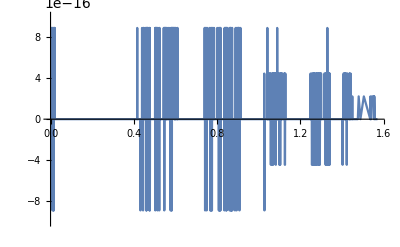

-Cos[α]-Cos[β]+2 √Cos[α] √Cos[β] √Cos[γ]+Cos[γ]-2 Cos[α] Cos[γ]-2 Cos[β] Cos[γ]+4 √Cos[α] √Cos[β] Cos[γ]^(3/2)-2 Cos[γ]^2+2 √(Cos[γ]+Cos[γ]^2)-2 Cos[α] √(Cos[γ]+Cos[γ]^2)-2 Cos[β] √(Cos[γ]+Cos[γ]^2)+4 √Cos[α] √Cos[β] √Cos[γ] √(Cos[γ]+Cos[γ]^2)-2 Cos[γ] √(Cos[γ]+Cos[γ]^2)

10.4 (1-Cos[aa]-Cos[bb]+2 √Cos[aa] √Cos[bb] √Cos[gc]-Cos[gc]) (1+2 Cos[gc]+2 √(Cos[gc]+Cos[gc]^2))+8.45 x (1-Cos[aa]-Cos[bb]+2 √Cos[aa] √Cos[bb] √Cos[gc]-Cos[gc]) (1+2 Cos[gc]+2 √(Cos[gc]+Cos[gc]^2))-109.85 x^2 (1-Cos[aa]-Cos[bb]+2 √Cos[aa] √Cos[bb] √Cos[gc]-Cos[gc]) (1+2 Cos[gc]+2 √(Cos[gc]+Cos[gc]^2))+(-1+(1-Cos[aa]-Cos[bb]+2 √Cos[aa] √Cos[bb] √Cos[gc]-Cos[gc]) (1+2 Cos[gc]+2 √(Cos[gc]+Cos[gc]^2)))/x

-1+1. (1-Cos[α]-Cos[β]+2 √Cos[α] √Cos[β] √Cos[γ]-Cos[γ]) (1+2 Cos[γ]+2 √(Cos[γ]+Cos[γ]^2))

0.+10.4 (1-Cos[α]-Cos[β]+2 √Cos[α] √Cos[β] √Cos[γ]-Cos[γ]) (1+2 Cos[γ]+2 √(Cos[γ]+Cos[γ]^2))+8.45 x (1-Cos[α]-Cos[β]+2 √Cos[α] √Cos[β] √Cos[γ]-Cos[γ]) (1+2 Cos[γ]+2 √(Cos[γ]+Cos[γ]^2))-109.85 x^2 (1-Cos[α]-Cos[β]+2 √Cos[α] √Cos[β] √Cos[γ]-Cos[γ]) (1+2 Cos[γ]+2 √(Cos[γ]+Cos[γ]^2))

```mathematica
(*Expression for Volume change with symmetry restriction*)
Solve[r-1==2*Sqrt[r*Cos[γ]],r]
Plot[1+2 √2 Cos[γ/2] √Cos[γ]+2 Cos[γ]-(2*Cos[γ]+1+2*Sqrt[Cos[γ]+Cos[γ]^2]),{γ,0,Pi/2},PlotRange->{-10^-15,10^-15}](*Checking if the root returned above matches the expression we derived in OneNote/Effect of stress on transition temperature/LSCO/Tetragonal to triclinic *)
(2*Cos[γ]+1+2*Sqrt[Cos[γ]+Cos[γ]^2])*(1-Cos[α]-Cos[β]+2*√Cos[α] √Cos[β] √Cos[γ]-Cos[γ])-1//Expand
dv[x_,aa_,bb_,gc_]:=(1+6.5*x)^2*(1-2.6*x)*(2*Cos[gc]+1+2*Sqrt[Cos[gc]+Cos[gc]^2])*(1-Cos[aa]-Cos[bb]+2*√Cos[aa] √Cos[bb] √Cos[gc]-Cos[gc])-1
Collect[dv[x,aa,bb,gc]/x,x]
dv[0,α,β,γ](*This is the O(1) term for Tetragonal to Triclinic phase transition which must vanish.*)
Collect[(dv[x,α,β,γ]-dv[0,α,β,γ])/x,x](*This is the O(1) term for Tetragonal to Triclinic phase transition which must vanish.*)
```